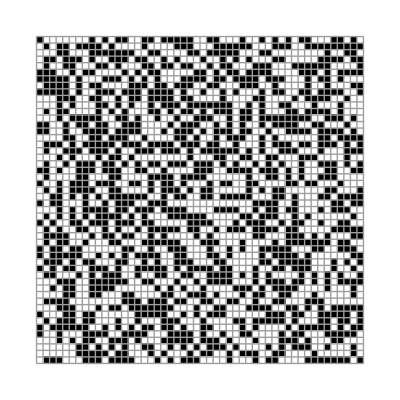

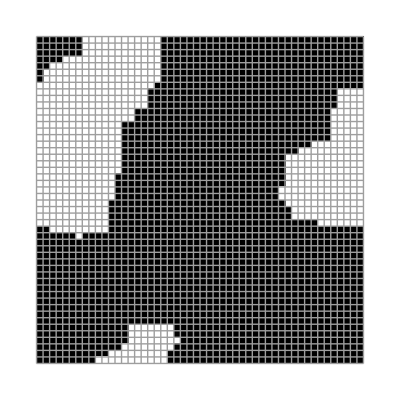

-Graphics-

```mathematica
(* 
  June 24^th, 2011

Two-Dimensional Ising Model

Here simulated is a 50x50 2-D Ising lattice on a torus. The magnetic spins are flipped according to the metropolis algorithm,         vying for lower energy states. An array of black/white squares is generated to visualize the state of the system at various temperatures and time steps.

The magnetization per spin is calculated and plotted. Then, the magnetic susceptibility is calculated and plotted.

  n = number of columns
  m = number of rows
 T = temperature
*)

n=50;
m=50;
maxT = 3;
minT = 0.00001;
diffT = -0.00001;


initial = Table[If[Random[] < 0.5,-1,1],{i,1,n},{j,1,m}];

ArrayPlot[initial,ColorRules->{-1->White,1->Black},Mesh -> True]

config = initial;

nboundary[i_] := 1 + Mod[i-1,n]
mboundary[j_] := 1 + Mod[j-1,m]

magnetevolution := (
	
		nspin = Ceiling[Random[]*n];

		mspin = Ceiling[Random[]*m];

                            change = 
2*1/T*config[[nspin,mspin]]*(  config[[nboundary[nspin-1],mspin]]+
						      config[[nboundary[nspin+1],mspin]]+
					               config[[nspin,mboundary[mspin-1]]]+
					               config[[nspin,mboundary[mspin+1]]]  ) ;

probability = Exp[-change];

metropolis = If[ change ≤ 0,config[[nspin,mspin]] = -config[[nspin,mspin]],acceptance];

acceptance := If[ Random[] < probability, 
                              config[[nspin,mspin]] = -config[[nspin,mspin]],
                             config[[nspin,mspin]] = config[[nspin,mspin]]  ] ;

config[[nspin,mspin]];

upspins = Count[Flatten[config],1];
spinmag = (2*upspins)/(n*m)-1 

)
                         
magnettable= Table[magnetevolution,{T,maxT,minT,diffT}];
array = ArrayPlot[config,ColorRules->{-1->White,1->Black},Mesh -> True]

ListPlot[magnettable]
```